```mathematica
(*Using non linear multiscale cascades so peark formation emerges from it rather than it being additive to the base*)
ClearAll["Global`*"];
$HistoryLength=0;
```

```mathematica
ClearAll[GenerateEndogenousForcingBase];

Options[GenerateEndogenousForcingBase]={"MeanForcing"->0.03,"ForcingVariation"->0.25,"RandomMethod"->"MersenneTwister"};

GenerateEndogenousForcingBase[seed_Integer,length_Integer?Positive,OptionsPattern[]]:=Module[{meanForcing,forcingVariation,randomMethod,randomStreams,forcingInnovation,observationCarrier,coarseForcing,forcingLowerBound,forcingUpperBound},meanForcing=N@OptionValue["MeanForcing"];
forcingVariation=N@OptionValue["ForcingVariation"];
randomMethod=OptionValue["RandomMethod"];
If[meanForcing<=0.,Return[Failure["InvalidMeanForcing",<|"Message"->"MeanForcing must be positive."|>]]];
If[forcingVariation<0.||forcingVariation>=1.,Return[Failure["InvalidForcingVariation",<|"Message"->"ForcingVariation must satisfy 0 <= variation < 1."|>]]];
(*Generate two deterministic streams from one seed:stream 1:coarse forcing fluctuations stream 2:signed observation carrier used later They are generated together so the complete model needs only one external seed.*)randomStreams=BlockRandom[SeedRandom[seed,Method->randomMethod];
RandomVariate[NormalDistribution[0.,1.],{2,length}]];
forcingInnovation=randomStreams[[1]];
observationCarrier=randomStreams[[2]];
(*Bounded continuous activity injection.Since-1<Tanh[z]<1:F0 (1-variation)<forcing<F0 (1+variation)*)coarseForcing=meanForcing*(1.+forcingVariation Tanh[forcingInnovation]);
forcingLowerBound=meanForcing (1.-forcingVariation);
forcingUpperBound=meanForcing (1.+forcingVariation);
<|"Model"->"EndogenousOneDimensionalTurbulence","Stage"->"BoundedContinuousCoarseForcing","Version"->"1.0.0","Seed"->seed,"Length"->length,"ForcingInnovation"->forcingInnovation,"ObservationCarrier"->observationCarrier,"CoarseForcing"->coarseForcing,"Parameters"-><|"MeanForcing"->meanForcing,"ForcingVariation"->forcingVariation,"ForcingLowerBound"->forcingLowerBound,"ForcingUpperBound"->forcingUpperBound,"RandomMethod"->randomMethod,"ForcingMemory"->"None","ImposedPeakFrequency"->"None","ImposedPeakSeverity"->"None"|>|>];
```

```mathematica
endogenousSeed=20260817;

endogenousLength=8192;

endogenousMeanForcing=0.03;

endogenousForcingVariation=0.25;

endogenousForcingBase=GenerateEndogenousForcingBase[endogenousSeed,endogenousLength,"MeanForcing"->endogenousMeanForcing,"ForcingVariation"->endogenousForcingVariation];
```

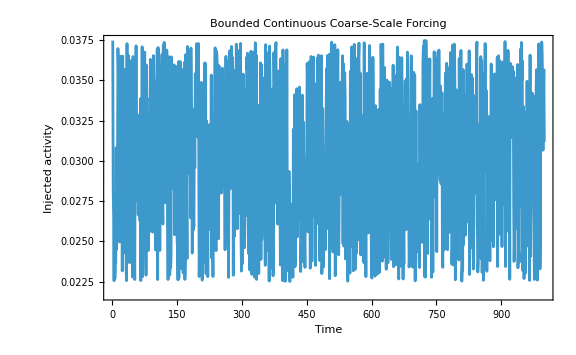

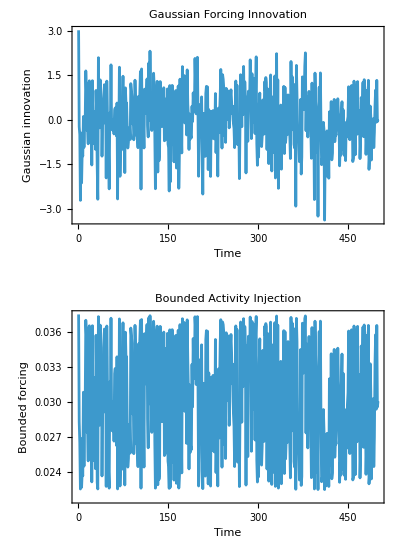

```mathematica
endogenousForcingPlot=ListLinePlot[Take[endogenousForcingBase["CoarseForcing"],1000],PlotRange->All,Frame->True,FrameLabel->{"Time","Injected activity"},PlotLabel->"Bounded Continuous Coarse-Scale Forcing",ImageSize->Large];
endogenousForcingPlot
forcingTransformationPlot=GraphicsColumn[{ListLinePlot[Take[endogenousForcingBase["ForcingInnovation"],500],PlotRange->All,Frame->True,FrameLabel->{"Time","Gaussian innovation"},PlotLabel->"Gaussian Forcing Innovation",ImageSize->Large],ListLinePlot[Take[endogenousForcingBase["CoarseForcing"],500],PlotRange->All,Frame->True,FrameLabel->{"Time","Bounded forcing"},PlotLabel->"Bounded Activity Injection",ImageSize->Large]}];
forcingTransformationPlot
```

```mathematica
ClearAll[AddCoarseStorageRelease];

Options[AddCoarseStorageRelease]={"OpenThreshold"->2.0,"CloseThreshold"->0.40,"GateResponse"->0.30,"MaximumReleaseFraction"->0.45,"NonlinearReference"->2.0,"BackgroundDissipationRate"->0.002};

AddCoarseStorageRelease[forcingBase_Association,OptionsPattern[]]:=Module[{openThreshold,closeThreshold,gateResponse,maximumReleaseFraction,nonlinearReference,backgroundDissipationRate,coarseForcing,initialState,storageStep,stateHistory,coarseEnergy,transferGate,gateLatch,releaseFlux,backgroundDissipation},openThreshold=N@OptionValue["OpenThreshold"];
closeThreshold=N@OptionValue["CloseThreshold"];
gateResponse=N@OptionValue["GateResponse"];
maximumReleaseFraction=N@OptionValue["MaximumReleaseFraction"];
nonlinearReference=N@OptionValue["NonlinearReference"];
backgroundDissipationRate=N@OptionValue["BackgroundDissipationRate"];
If[closeThreshold<0.||openThreshold<=closeThreshold,Return[Failure["InvalidThresholds",<|"Message"->"OpenThreshold must be greater than CloseThreshold, and both must be non-negative."|>]]];
If[gateResponse<=0.||gateResponse>1.,Return[Failure["InvalidGateResponse",<|"Message"->"GateResponse must satisfy 0 < response <= 1."|>]]];
If[maximumReleaseFraction<0.||backgroundDissipationRate<0.||maximumReleaseFraction+backgroundDissipationRate>1.,Return[Failure["InvalidActivityBudget",<|"Message"->"Maximum release plus background dissipation cannot exceed one."|>]]];
If[nonlinearReference<=0.,Return[Failure["InvalidNonlinearReference",<|"Message"->"NonlinearReference must be positive."|>]]];
coarseForcing=forcingBase["CoarseForcing"];
(*State vector:1. stored coarse energy 2. continuous gate position 3. hysteretic gate latch 4. release flux generated during the step 5. background dissipation during the step*)initialState={0.,0.,0.,0.,0.};
storageStep[state_List,forcing_?NumericQ]:=Module[{energy,gate,latch,nextLatch,nextGate,nonlinearActivation,currentRelease,currentDissipation,nextEnergy},energy=state[[1]];
gate=state[[2]];
latch=state[[3]];
(*Hysteresis:open at the upper threshold remain open between thresholds close at the lower threshold*)nextLatch=Which[energy>=openThreshold,1.,energy<=closeThreshold,0.,True,latch];
(*The gate approaches its target gradually.*)nextGate=Clip[gate+gateResponse (nextLatch-gate),{0.,1.}];
(*Low activity:release approximately proportional to E^(3/2) High activity:release remains below MaximumReleaseFraction E*)nonlinearActivation=Sqrt[energy/nonlinearReference]/(1.+Sqrt[energy/nonlinearReference]);
currentRelease=maximumReleaseFraction*nextGate*energy*nonlinearActivation;
currentDissipation=backgroundDissipationRate energy;
nextEnergy=Max[0.,energy+forcing-currentRelease-currentDissipation];
{nextEnergy,nextGate,nextLatch,currentRelease,currentDissipation}];
stateHistory=Rest@FoldList[storageStep,initialState,coarseForcing];
coarseEnergy=stateHistory[[All,1]];
transferGate=stateHistory[[All,2]];
gateLatch=stateHistory[[All,3]];
releaseFlux=stateHistory[[All,4]];
backgroundDissipation=stateHistory[[All,5]];
Join[forcingBase,<|"Stage"->"HystereticCoarseStorageRelease","Version"->"1.1.0","ParentStage"->"BoundedContinuousCoarseForcing","CoarseEnergy"->coarseEnergy,"TransferGate"->transferGate,"GateLatch"->gateLatch,"CoarseReleaseFlux"->releaseFlux,"CoarseDissipation"->backgroundDissipation,(*Stable cascade interface*)"ScaleStates"->List/@coarseEnergy,"TransferFluxes"->List/@releaseFlux,"DissipationFluxes"->List/@backgroundDissipation,"Parameters"->Join[forcingBase["Parameters"],<|"OpenThreshold"->openThreshold,"CloseThreshold"->closeThreshold,"GateResponse"->gateResponse,"MaximumReleaseFraction"->maximumReleaseFraction,"NonlinearReference"->nonlinearReference,"BackgroundDissipationRate"->backgroundDissipationRate,"PeakTimingRule"->"None: release is activated by stored activity"|>]|>]];
```

```mathematica
coarseOpenThreshold=2.0;

coarseCloseThreshold=0.40;

coarseGateResponse=0.30;

coarseMaximumReleaseFraction=0.45;

coarseNonlinearReference=2.0;

coarseBackgroundDissipationRate=0.002;

coarseStorageCore=AddCoarseStorageRelease[endogenousForcingBase,"OpenThreshold"->coarseOpenThreshold,"CloseThreshold"->coarseCloseThreshold,"GateResponse"->coarseGateResponse,"MaximumReleaseFraction"->coarseMaximumReleaseFraction,"NonlinearReference"->coarseNonlinearReference,"BackgroundDissipationRate"->coarseBackgroundDissipationRate];
```

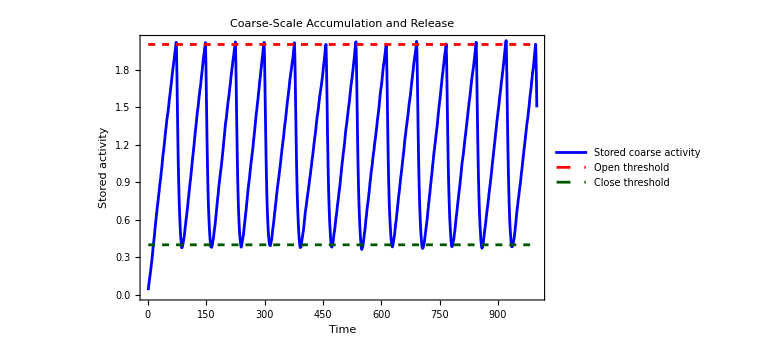

```mathematica
coarseStorageWindow=1000;

coarseEnergyPlot=ListLinePlot[{Take[coarseStorageCore["CoarseEnergy"],coarseStorageWindow],ConstantArray[coarseOpenThreshold,coarseStorageWindow],ConstantArray[coarseCloseThreshold,coarseStorageWindow]},PlotLegends->{"Stored coarse activity","Open threshold","Close threshold"},PlotStyle->{Blue,Directive[Red,Dashed],Directive[DarkGreen,Dashed]},PlotRange->All,Frame->True,FrameLabel->{"Time","Stored activity"},PlotLabel->"Coarse-Scale Accumulation and Release",ImageSize->Large];

coarseEnergyPlot
```

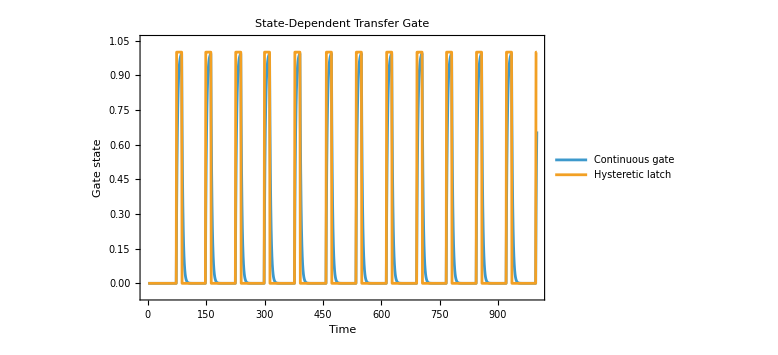

```mathematica
coarseGatePlot=ListLinePlot[{Take[coarseStorageCore["TransferGate"],coarseStorageWindow],Take[coarseStorageCore["GateLatch"],coarseStorageWindow]},PlotLegends->{"Continuous gate","Hysteretic latch"},PlotRange->{All,{-0.05,1.05}},Frame->True,FrameLabel->{"Time","Gate state"},PlotLabel->"State-Dependent Transfer Gate",ImageSize->Large];

coarseGatePlot
```

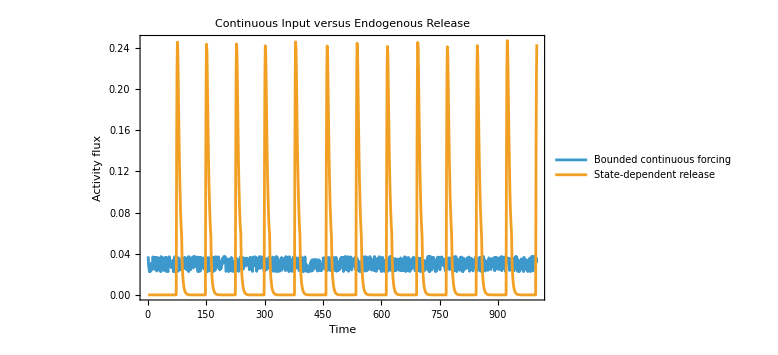

```mathematica
coarseReleasePlot=ListLinePlot[{Take[coarseStorageCore["CoarseForcing"],coarseStorageWindow],Take[coarseStorageCore["CoarseReleaseFlux"],coarseStorageWindow]},PlotLegends->{"Bounded continuous forcing","State-dependent release"},PlotRange->All,Frame->True,FrameLabel->{"Time","Activity flux"},PlotLabel->"Continuous Input versus Endogenous Release",ImageSize->Large];

coarseReleasePlot
```

```mathematica
ClearAll[AddInteractingMultiscaleReservoirs];

Options[AddInteractingMultiscaleReservoirs]={"OpenThresholds"->{1.80,0.45,0.12},"CloseThresholds"->{0.45,0.10,0.025},"GateResponses"->{0.22,0.35,0.55},"MaximumTransferFractions"->{0.45,0.60,0.75},"NonlinearReferences"->{1.80,0.45,0.12},"DownstreamCapacities"->{0.60,0.20,0.06},"ResistancePowers"->{4.,4.,4.},"DissipationRates"->{0.002,0.015,0.06,0.40}};

AddInteractingMultiscaleReservoirs[forcingBase_Association,OptionsPattern[]]:=Module[{openThresholds,closeThresholds,gateResponses,maximumTransferFractions,nonlinearReferences,downstreamCapacities,resistancePowers,dissipationRates,numberOfScales,numberOfTransfers,coarseForcing,initialState,interactionStep,stateHistory,scaleStates,transferGates,gateLatches,transferFluxes,dissipationFluxes,downstreamAvailabilities,fineScaleDissipation},openThresholds=N@OptionValue["OpenThresholds"];
closeThresholds=N@OptionValue["CloseThresholds"];
gateResponses=N@OptionValue["GateResponses"];
maximumTransferFractions=N@OptionValue["MaximumTransferFractions"];
nonlinearReferences=N@OptionValue["NonlinearReferences"];
downstreamCapacities=N@OptionValue["DownstreamCapacities"];
resistancePowers=N@OptionValue["ResistancePowers"];
dissipationRates=N@OptionValue["DissipationRates"];
numberOfScales=Length[dissipationRates];
numberOfTransfers=numberOfScales-1;
If[!SameQ[Length/@{openThresholds,closeThresholds,gateResponses,maximumTransferFractions,nonlinearReferences,downstreamCapacities,resistancePowers},ConstantArray[numberOfTransfers,7]],Return[Failure["InvalidCascadeDimensions",<|"Message"->"Every transfer parameter must have one fewer element than DissipationRates."|>]]];
If[!And@@MapThread[Greater,{openThresholds,closeThresholds}],Return[Failure["InvalidThresholds",<|"Message"->"Every opening threshold must exceed its closing threshold."|>]]];
If[!AllTrue[gateResponses,0.<#<=1.&],Return[Failure["InvalidGateResponse",<|"Message"->"Every gate response must satisfy 0 < response <= 1."|>]]];
If[!AllTrue[Join[nonlinearReferences,downstreamCapacities,resistancePowers],#>0.&],Return[Failure["InvalidPositiveParameter",<|"Message"->"References, capacities, and resistance powers must be positive."|>]]];
If[!AllTrue[MapThread[Plus,{dissipationRates,Append[maximumTransferFractions,0.]}],#<=1.&],Return[Failure["InvalidActivityBudget",<|"Message"->"Dissipation plus maximum outgoing transfer cannot exceed one."|>]]];
coarseForcing=forcingBase["CoarseForcing"];
initialState=<|"Energy"->ConstantArray[0.,numberOfScales],"Gate"->ConstantArray[0.,numberOfTransfers],"Latch"->ConstantArray[0.,numberOfTransfers],"TransferFlux"->ConstantArray[0.,numberOfTransfers],"DissipationFlux"->ConstantArray[0.,numberOfScales],"DownstreamAvailability"->ConstantArray[1.,numberOfTransfers]|>;
interactionStep[state_Association,forcing_?NumericQ]:=Module[{energy,gate,latch,nextLatch,nextGate,nonlinearActivation,downstreamAvailability,currentTransferFlux,currentDissipation,nextEnergy},energy=state["Energy"];
gate=state["Gate"];
latch=state["Latch"];
(*Each transfer gate has its own hysteresis.*)nextLatch=MapThread[Function[{upstreamEnergy,openThreshold,closeThreshold,previousLatch},Which[upstreamEnergy>=openThreshold,1.,upstreamEnergy<=closeThreshold,0.,True,previousLatch]],{Most[energy],openThresholds,closeThresholds,latch}];
nextGate=MapThread[Function[{previousGate,targetLatch,response},Clip[previousGate+response (targetLatch-previousGate),{0.,1.}]],{gate,nextLatch,gateResponses}];
(*Nonlinear activation is approximately E^(1/2) at low activity.Multiplication by E below makes the resulting flux approximately E^(3/2).*)nonlinearActivation=MapThread[Function[{upstreamEnergy,reference},Sqrt[upstreamEnergy/reference]/(1.+Sqrt[upstreamEnergy/reference])],{Most[energy],nonlinearReferences}];
(*A loaded downstream scale resists incoming transfer.*)downstreamAvailability=MapThread[Function[{downstreamEnergy,capacity,resistancePower},1./(1.+(downstreamEnergy/capacity)^resistancePower)],{Rest[energy],downstreamCapacities,resistancePowers}];
currentTransferFlux=maximumTransferFractions*nextGate*Most[energy]*nonlinearActivation*downstreamAvailability;
currentDissipation=dissipationRates energy;
(*Simultaneous conservative transfer:outgoing activity leaves one scale and enters the next scale*)nextEnergy=energy-currentDissipation-Append[currentTransferFlux,0.]+Prepend[currentTransferFlux,0.];
nextEnergy[[1]]+=forcing;
nextEnergy=Map[Max[0.,#]&,nextEnergy];
<|"Energy"->nextEnergy,"Gate"->nextGate,"Latch"->nextLatch,"TransferFlux"->currentTransferFlux,"DissipationFlux"->currentDissipation,"DownstreamAvailability"->downstreamAvailability|>];
stateHistory=Rest@FoldList[interactionStep,initialState,coarseForcing];
scaleStates=(#["Energy"]&)/@stateHistory;
transferGates=(#["Gate"]&)/@stateHistory;
gateLatches=(#["Latch"]&)/@stateHistory;
transferFluxes=(#["TransferFlux"]&)/@stateHistory;
dissipationFluxes=(#["DissipationFlux"]&)/@stateHistory;
downstreamAvailabilities=(#["DownstreamAvailability"]&)/@stateHistory;
fineScaleDissipation=dissipationFluxes[[All,-1]];
Join[forcingBase,<|"Stage"->"InteractingMultiscaleReservoirs","Version"->"1.2.0","ParentStage"->"BoundedContinuousCoarseForcing","ReplacesStage"->"HystereticCoarseStorageRelease","ScaleStates"->scaleStates,"TransferGates"->transferGates,"GateLatches"->gateLatches,"TransferFluxes"->transferFluxes,"DissipationFluxes"->dissipationFluxes,"DownstreamAvailabilities"->downstreamAvailabilities,"FineScaleDissipation"->fineScaleDissipation,"CascadeActivity"->fineScaleDissipation,"Parameters"->Join[forcingBase["Parameters"],<|"NumberOfScales"->numberOfScales,"OpenThresholds"->openThresholds,"CloseThresholds"->closeThresholds,"GateResponses"->gateResponses,"MaximumTransferFractions"->maximumTransferFractions,"NonlinearReferences"->nonlinearReferences,"DownstreamCapacities"->downstreamCapacities,"ResistancePowers"->resistancePowers,"DissipationRates"->dissipationRates,"PeakTimingRule"->"None: fine-scale bursts emerge from interacting states"|>]|>]];
interactingCascadeCore=AddInteractingMultiscaleReservoirs[endogenousForcingBase,"OpenThresholds"->{1.80,0.45,0.12},"CloseThresholds"->{0.45,0.10,0.025},"GateResponses"->{0.22,0.35,0.55},"MaximumTransferFractions"->{0.45,0.60,0.75},"NonlinearReferences"->{1.80,0.45,0.12},"DownstreamCapacities"->{0.60,0.20,0.06},"ResistancePowers"->{4.,4.,4.},"DissipationRates"->{0.002,0.015,0.06,0.40}];
Head[interactingCascadeCore]
```

Association

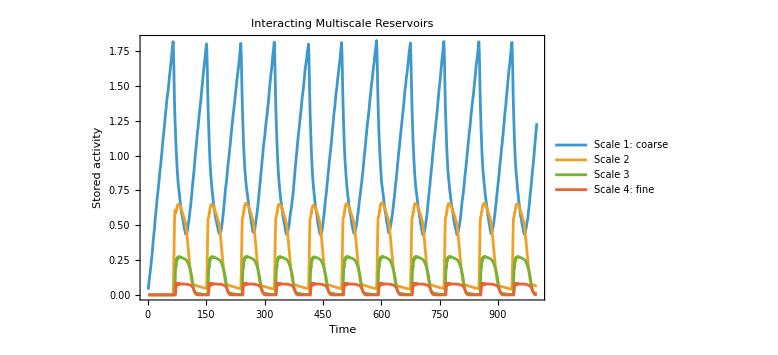

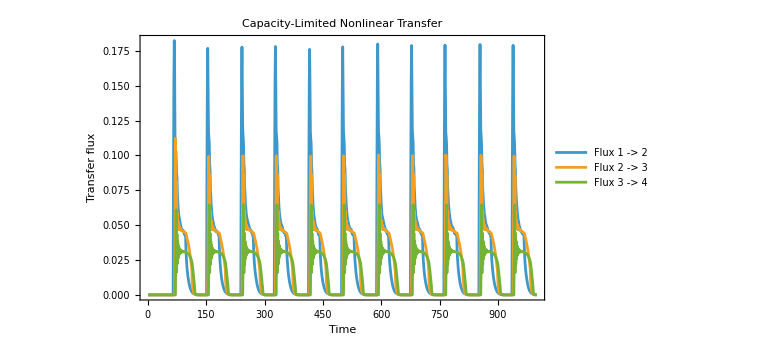

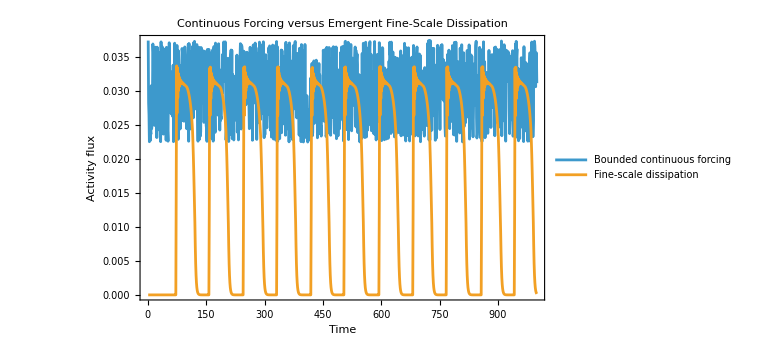

```mathematica
interactingCascadeWindow=1000;
interactingCascadeStatePlot=ListLinePlot[Transpose[Take[interactingCascadeCore["ScaleStates"],interactingCascadeWindow]],PlotLegends->{"Scale 1: coarse","Scale 2","Scale 3","Scale 4: fine"},PlotRange->All,Frame->True,FrameLabel->{"Time","Stored activity"},PlotLabel->"Interacting Multiscale Reservoirs",ImageSize->Large];
interactingCascadeStatePlot
interactingCascadeFluxPlot=ListLinePlot[Transpose[Take[interactingCascadeCore["TransferFluxes"],interactingCascadeWindow]],PlotLegends->{"Flux 1 -> 2","Flux 2 -> 3","Flux 3 -> 4"},PlotRange->All,Frame->True,FrameLabel->{"Time","Transfer flux"},PlotLabel->"Capacity-Limited Nonlinear Transfer",ImageSize->Large];
interactingCascadeFluxPlot
interactingCascadeDissipationPlot=ListLinePlot[{Take[interactingCascadeCore["CoarseForcing"],interactingCascadeWindow],Take[interactingCascadeCore["FineScaleDissipation"],interactingCascadeWindow]},PlotLegends->{"Bounded continuous forcing","Fine-scale dissipation"},PlotRange->All,Frame->True,FrameLabel->{"Time","Activity flux"},PlotLabel->"Continuous Forcing versus Emergent Fine-Scale Dissipation",ImageSize->Large];
interactingCascadeDissipationPlot
```

```mathematica
projectDirectory="/home/vinayakarora/Working-Dir/Turbulence";

exportTimestamp=DateString[{"Year","Month","Day","-","Hour","Minute","Second"}];

currentGraphExportDirectory=FileNameJoin[{projectDirectory,"exports","endogenous-reservoirs-"<>exportTimestamp}];

CreateDirectory[currentGraphExportDirectory,CreateIntermediateDirectories->True];
currentCascadeGraphs=<|"interacting-multiscale-reservoirs"->interactingCascadeStatePlot,"capacity-limited-nonlinear-transfer"->interactingCascadeFluxPlot,"forcing-versus-fine-scale-dissipation"->interactingCascadeDissipationPlot|>;
currentGraphPNGFiles=Association@KeyValueMap[Function[{graphName,graph},graphName->Export[FileNameJoin[{currentGraphExportDirectory,graphName<>".png"}],graph,ImageResolution->300]],currentCascadeGraphs];
currentGraphPDFFiles=Association@KeyValueMap[Function[{graphName,graph},graphName->Export[FileNameJoin[{currentGraphExportDirectory,graphName<>".pdf"}],graph]],currentCascadeGraphs];
currentGraphsCombined=GraphicsColumn[Values[currentCascadeGraphs],Spacings->20,ImageSize->1200];
currentGraphsCombinedPDF=Export[FileNameJoin[{currentGraphExportDirectory,"endogenous-reservoir-results.pdf"}],currentGraphsCombined];
currentGraphManifest=<|"ExportedAt"->DateString["ISODateTime"],"Model"->interactingCascadeCore["Model"],"Stage"->interactingCascadeCore["Stage"],"Version"->interactingCascadeCore["Version"],"Seed"->interactingCascadeCore["Seed"],"Length"->interactingCascadeCore["Length"],"PNGFiles"->currentGraphPNGFiles,"PDFFiles"->currentGraphPDFFiles,"CombinedPDF"->currentGraphsCombinedPDF|>;
Export[FileNameJoin[{currentGraphExportDirectory,"graph-manifest.json"}],currentGraphManifest,"JSON"];
Dataset[<|"ExportDirectory"->currentGraphExportDirectory,"PNGFiles"->currentGraphPNGFiles,"PDFFiles"->currentGraphPDFFiles,"CombinedPDF"->currentGraphsCombinedPDF|>]
```